```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Tally[{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}]
```

{{imp11,3},{imp,58},{imp2,3},{imp8,3},{imp5,3},{imp1,3},{imp10,3},{imp3,3},{imp14,3},{imp6,3},{imp7,3},{imp4,3},{imp12,3},{imp13,3},{imp9,3}}

```mathematica
0.023/0.46
```

0.05

```mathematica
pris:=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

```mathematica
pris
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
misfit[ϵ1_,ϵ2_,ϵ3_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,If[tra1>3,3,tra1]},{ω,Range[0,1.5,0.01]}];
v1=Module[{},
ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/2/2na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2,0,ρ2},{1.4,0.6,ρ3},{1,1,ρ4},{0.6,1.4,ρ5},{0,2,ρ6}};
list];v2=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/3/na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{3,0,ρ2},{2,1,ρ3},{1.5,1.5,ρ4},{1,2,ρ5},{0,3,ρ6}};
list];v3=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/4/4na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/4/4na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={(*{4,0,Log[ρ2},*){3,1,ρ3},{2,2,ρ4},{1,3,ρ5}(*,{0,4,Log[ρ6}*)};
list];
v0=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(-m5[[1;;150,2]]+ pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{0,0,ρ2}};
list];v5=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/5/5na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/5/5na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={(*{5,0,ρ2},{5*0.7,5*0.3,Log[ρ3},*){2.5,2.5,ρ4}(*,{5*0.3,5*0.7,ρ5},{0,5,ρ6}*)};
list];v6=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/6/6na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/6/6na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/6/6na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/6/6na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/6/6na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={(*{6,0,ρ2},{5*0.7,6*0.3,Log[ρ3},*){3,3,ρ4}(*,{6*0.3,6*0.7,ρ5},{0,6,ρ6}*)};
list];v7=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/1/1na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{1,0,ρ2},{1*0.7,1*0.3,ρ3},{.5,0.5,ρ4},{1*0.3,1*0.7,ρ5},{0,1,ρ6}};
list];
{v1,v2,v3,v0,v5,v6,v7}]
```

```mathematica
misfit[0.3,0.9,0,0.9,1.4]
```

{{{2,0,0.00107026},{1.4,0.6,0.000760644},{1,1,0.000621554},{0.6,1.4,0.000967224},{0,2,0.00652601}},{{3,0,0.0013902},{2,1,0.001085},{1.5,1.5,0.000773792},{1,2,0.000572168},{0,3,0.00445982}},{{3,1,0.00132295},{2,2,0.00104426},{1,3,0.000622411}},{{0,0,0.0169899}},{{2.5,2.5,0.00122519}},{{3,3,0.00136566}},{{1,0,0.000940084},{0.7,0.3,0.0010999},{0.5,0.5,0.001696},{0.3,0.7,0.00321999},{0,1,0.00995182}}}

Show::gcomb: Could not combine the graphics objects in ….

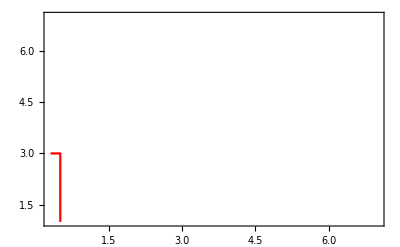
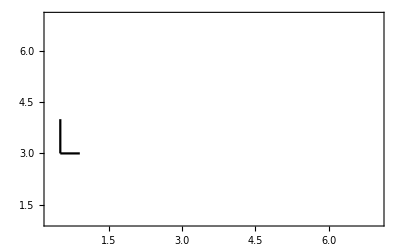
Show[%205,-Graphics-,-Graphics-]

```mathematica
Show[%205,ListLinePlot[{Table[{0.5,y},{y,Range[1,3.05,0.075]}],Table[{y,3},{y,Range[0.3,0.5,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}},PlotRange->{{0.3,7},{1,7}},Frame->True],ListLinePlot[{Table[{0.5,y},{y,Range[3,4,0.001]}],Table[{y,3},{y,Range[0.5,0.9,0.001]}]},PlotStyle->{{Dashing[{2*^-2,0.01,0.01,2*^-2}],Black},{Dashing[{2*^-2,0.01,0.01,2*^-2}],Black}},PlotRange->{{0.3,7},{1,7}},Frame->True]](*
Show[ContourPlot[Interpolation[bb2][x,y],{x,1,3},{y,1,3}],ListLinePlot[{Table[{0.5,y},{y,Range[0,7.5,0.075]}],Table[{y,3},{y,Range[0,4,0.075]}]},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red},{Dashing[{1*^-2,0.01,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}},Frame->True]]*)
```

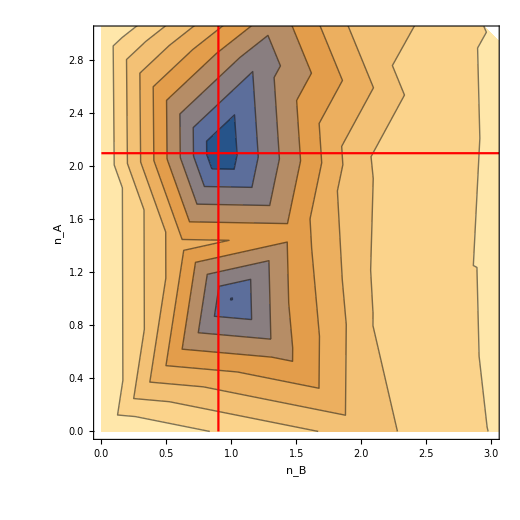

```mathematica
Show[%314,FrameLabel->{{HoldForm[Subscript[n, A]],None},{HoldForm[Subscript[n, B]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",17,GrayLevel[0]},ImageSize->{520,520}]
```

```mathematica
misfit[0.3,0.9,0,0,1.49]
```

{{{2,0,0.00202822},{1.4,0.6,0.00131071},{1,1,0.00100324},{0.6,1.4,0.00152878},{0,2,0.00904023}},{{3,0,0.00311076},{2,1,0.00223735},{1.5,1.5,0.00148894},{1,2,0.000999382},{0,3,0.00626164}},{{3,1,0.00305707},{2,2,0.00221462},{1,3,0.00123962}},{{0,0,0.0233639}},{{2.5,2.5,0.00282798}},{{3,3,0.00329471}},{{1,0,0.00123969},{0.7,0.3,0.00153195},{0.5,0.5,0.0024457},{0.3,0.7,0.00466899},{0,1,0.0136054}}}

```mathematica
aa=misfit[0.3,0.9,0,0,1.49]
bb1=Sort[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]],aa[[7]]]]
bb2=Sort[Join[aa[[8]],aa[[9]],aa[[10]],aa[[11]],aa[[12]],aa[[13]]]]
ListContourPlot[bb2,PlotRange->Automatic]
(*ContourPlot[ListInterpolation[bb1][x,y],{x,0,3},{y,0,3}]*)
```

{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}}

{{0,0,0.021475},{0,1,0.0118839},{0,2,0.0075132},{0,3,0.00500415},{0.3,0.7,0.00389141},{0.5,0.5,0.00210113},{0.6,1.4,0.00134271},{0.7,0.3,0.00148043},{1,0,0.00144497},{1,1,0.00126259},{1,2,0.00119407},{1,3,0.00158412},{1.4,0.6,0.00179334},{1.5,1.5,0.00196879},{2,0,0.00261633},{2,1,0.00280697},{2,2,0.00270454},{2.5,2.5,0.00323482},{3,0,0.00363626},{3,1,0.00352098},{3,3,0.00362029}}

Part::partw: Part 8 of {{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}} does not exist.

Part::partw: Part 9 of {{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}} does not exist.

Part::partw: Part 10 of {{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}} cannot be used as a part specification.

8⟦9,10,11,12,13,{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}}⟧

Part::pkspec1: The expression {{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}} cannot be used as a part specification.

ListContourPlot::arrayerr: 8.⟦9,10,11,12,13,«1»,{«1»},{«1»},{«1»},{{{2,0,0.00261633},«3»,{0,2,0.0075132}},«5»,«1»},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}}⟧ must be a valid array.

ListContourPlot[8⟦9,10,11,12,13,{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}},{{{2,0,0.00261633},{1.4,0.6,0.00179334},{1,1,0.00126259},{0.6,1.4,0.00134271},{0,2,0.0075132}},{{3,0,0.00363626},{2,1,0.00280697},{1.5,1.5,0.00196879},{1,2,0.00119407},{0,3,0.00500415}},{{3,1,0.00352098},{2,2,0.00270454},{1,3,0.00158412}},{{0,0,0.021475}},{{2.5,2.5,0.00323482}},{{3,3,0.00362029}},{{1,0,0.00144497},{0.7,0.3,0.00148043},{0.5,0.5,0.00210113},{0.3,0.7,0.00389141},{0,1,0.0118839}}}⟧,PlotRange→Automatic]

```mathematica
BubbleChart[bb1,ColorFunction->(RGBColor[#3,0,0]&)]
```

-Graphics-

```mathematica
ListPointPlot3D[bb1]
```

-Graphics3D-

```mathematica
Transpose[bb1][[1]]
```

{0,0,0,0,0.3,0.5,0.6,0.7,1,1,1,1,1.4,1.5,2,2,2,2.5,3,3,3}

```mathematica
Transpose[bb1][[2]]
```

{0,1,2,3,0.7,0.5,1.4,0.3,0,1,2,3,0.6,1.5,0,1,2,2.5,0,1,3}

```mathematica
Join[{%80},{%81}]
```

{{0,0,0,0,0.3,0.5,0.6,0.7,1,1,1,1,1.4,1.5,2,2,2,2.5,3,3,3},{0,1,2,3,0.7,0.5,1.4,0.3,0,1,2,3,0.6,1.5,0,1,2,2.5,0,1,3}}

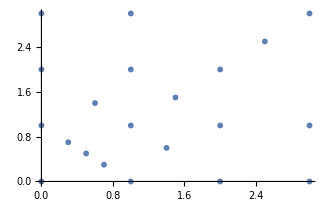

```mathematica
ListPlot[Transpose[{{0,0,0,0,0.3,0.5,0.6,0.7,1,1,1,1,1.4,1.5,2,2,2,2.5,3,3,3},{0,1,2,3,0.7,0.5,1.4,0.3,0,1,2,3,0.6,1.5,0,1,2,2.5,0,1,3}}]]
```

```mathematica
Transpose[{{0,0,0,0,0.3,0.5,0.6,0.7,0.9,1,1,1.2,1.4,1.5,2,2,2.1,2.5,2.8,3,3},{0,1,2,3,0.7,0.5,1.4,0.3,2.1,0,1,2.8,0.6,1.5,0,2,0.9,2.5,1.2,0,3}}]
```

{{0,0},{0,1},{0,2},{0,3},{0.3,0.7},{0.5,0.5},{0.6,1.4},{0.7,0.3},{0.9,2.1},{1,0},{1,1},{1.2,2.8},{1.4,0.6},{1.5,1.5},{2,0},{2,2},{2.1,0.9},{2.5,2.5},{2.8,1.2},{3,0},{3,3}}

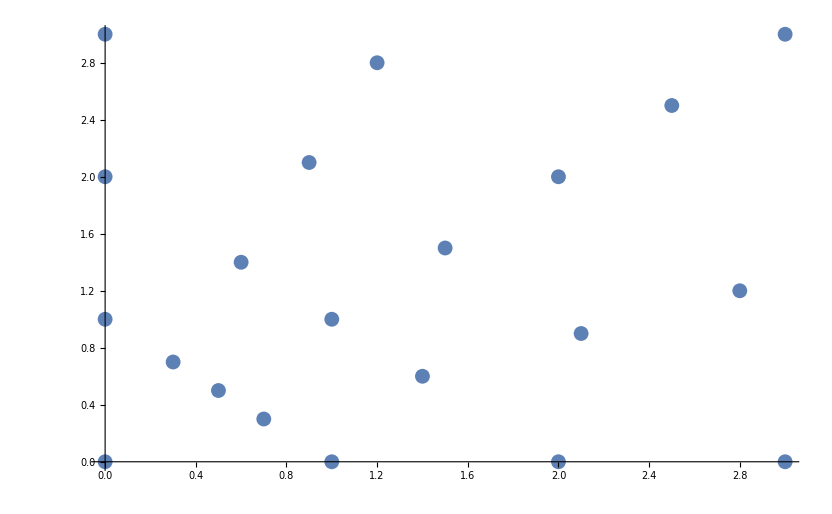

```mathematica
ListPlot[%71]
```

```mathematica
Transpose[Transpose[%56][[1]],Transpose[%56][[2]]]
```

Transpose::tperm: Permutation {0,1,2,3,0.7,0.5,1.4,0.3,2.1,0,1,2.8,0.6,1.5,0,2,0.9,2.5,1.2,0,3} is longer than the dimensions {21} of the expression.

Transpose[{0,0,0,0,0.3,0.5,0.6,0.7,0.9,1,1,1.2,1.4,1.5,2,2,2.1,2.5,2.8,3,3},{0,1,2,3,0.7,0.5,1.4,0.3,2.1,0,1,2.8,0.6,1.5,0,2,0.9,2.5,1.2,0,3}]

```mathematica
ListInterpolation[%56]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction[…]

```mathematica
Plot3D[%63[x,y],{x,1.,21.},{y,1.,3.}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[bb1]
```

-Graphics3D-

```mathematica
ListInterpolation[bb1]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction[…]

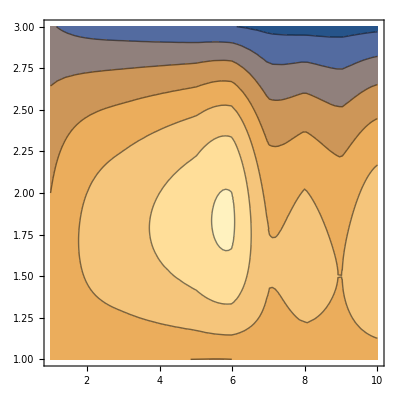

```mathematica
ContourPlot[%32[x,y],{x,1.,10.},{y,1.,3.}]
```

InterpolatingFunction::dmval: Input value {0.000214286,0.000214286} lies outside the range of data in the interpolating function. Extrapolation will be used.

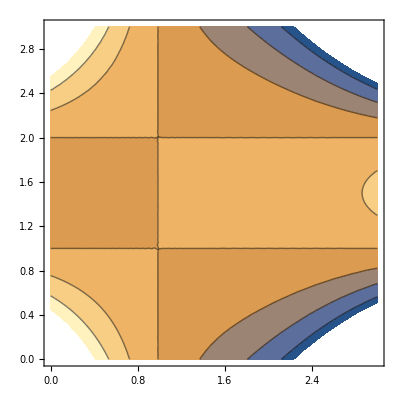

```mathematica
ContourPlot[%23[x,y],{x,0.,3.},{y,0.,3.}]
```

```mathematica
ListInterpolation[bb1]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction[…]

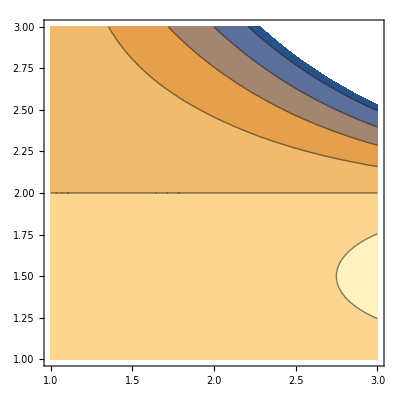

```mathematica
ContourPlot[%277[x,y],{x,1.,3.},{y,1.,3.}]
```

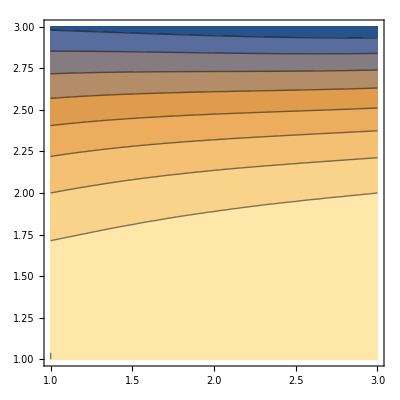

```mathematica
ContourPlot[%232[x,y],{x,1.,3.},{y,1.,3.}]
```

```mathematica
Transpose[{Transpose[%159][[1]],Transpose[%159][[2]],-Transpose[%159][[3]]}]
```

{{0.3,1,-4.45481},{0.3,2,-4.91745},{0.3,3,-5.33299},{0.3,4,-5.69578},{0.3,5,-6.00153},{0.3,6,-6.2406},{0.4,1,-4.88595},{0.4,2,-5.67787},{0.4,3,-6.3027},{0.4,4,-6.63835},{0.4,5,-6.67204},{0.4,6,-6.55101},{0.5,1,-5.40414},{0.5,2,-6.44913},{0.5,3,-6.70961},{0.5,4,-6.42331},{0.5,5,-6.09371},{0.5,6,-5.85805},{0.6,1,-5.88638},{0.6,2,-6.64902},{0.6,3,-6.30951},{0.6,4,-5.9378},{0.6,5,-5.69704},{0.6,6,-5.54078},{0.7,1,-6.26086},{0.7,2,-6.37341},{0.7,3,-5.8923},{0.7,4,-5.59196},{0.7,5,-5.43149},{0.7,6,-5.3333},{0.8,1,-6.38776},{0.8,2,-6.01969},{0.8,3,-5.61078},{0.8,4,-5.39598},{0.8,5,-5.2882},{0.8,6,-5.23201},{0.9,1,-6.32084},{0.9,2,-5.75129},{0.9,3,-5.427},{0.9,4,-5.2807},{0.9,5,-5.20996},{0.9,6,-5.17915}}

```mathematica
Interpolation[%166]
```

InterpolatingFunction[…]

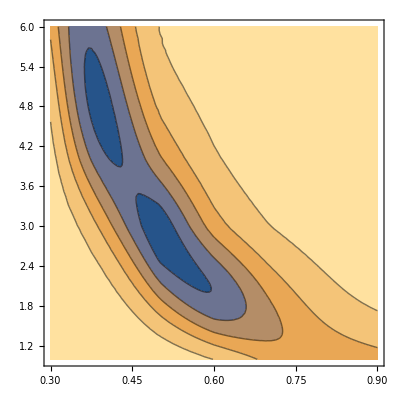

```mathematica
ContourPlot[%169[x,y]^13,{x,0.3,0.9},{y,1.,6.}]
```

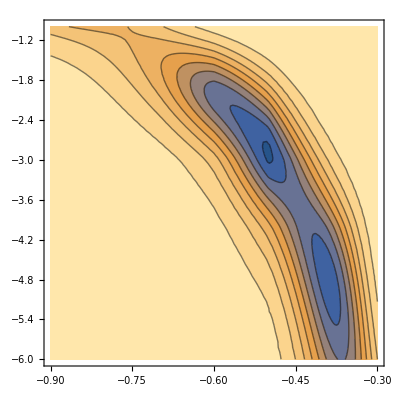

```mathematica
%160
```

```mathematica
f=Interpolation[-%831
```

InterpolatingFunction[…]^21

```mathematica
Interpolation[-%83]
```

InterpolatingFunction[…]

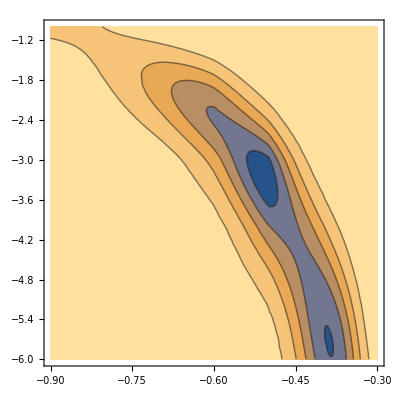

```mathematica
ContourPlot[Interpolation[-bb2][x,y7,{x,-0.9,-0.3},{y,-6.,-1.}]
```

```mathematica
f[-0.5,-4]
```

InterpolatingFunction[…]^21[-0.5,-4]

```mathematica
Table[{y,Interpolation[-%83][y,-31},{y,Range[-0.9,-0.3,0.01]}]
```

{{-0.9,-2.02113×10^15},{-0.89,-2.12336×10^15},{-0.88,-2.23559×10^15},{-0.87,-2.35912×10^15},{-0.86,-2.49541×10^15},{-0.85,-2.64613×10^15},{-0.84,-2.81322×10^15},{-0.83,-2.99889×10^15},{-0.82,-3.20573×10^15},{-0.81,-3.4367×10^15},{-0.8,-3.69526×10^15},{-0.79,-3.98544×10^15},{-0.78,-4.31193×10^15},{-0.77,-4.68026×10^15},{-0.76,-5.09687×10^15},{-0.75,-5.56939×10^15},{-0.74,-6.1068×10^15},{-0.73,-6.71974×10^15},{-0.72,-7.42086×10^15},{-0.71,-8.22517×10^15},{-0.7,-9.15065×10^15},{-0.69,-1.03672×10^16},{-0.68,-1.17784×10^16},{-0.67,-1.34084×10^16},{-0.66,-1.52824×10^16},{-0.65,-1.74258×10^16},{-0.64,-1.98638×10^16},{-0.63,-2.26192×10^16},{-0.62,-2.57118×10^16},{-0.61,-2.91558×10^16},{-0.6,-3.29579×10^16},{-0.59,-3.76021×10^16},{-0.58,-4.26709×10^16},{-0.57,-4.80962×10^16},{-0.56,-5.3772×10^16},{-0.55,-5.95503×10^16},{-0.54,-6.52404×10^16},{-0.53,-7.06122×10^16},{-0.52,-7.54052×10^16},{-0.51,-7.93424×10^16},{-0.5,-8.21502×10^16},{-0.49,-8.16489×10^16},{-0.48,-7.9743×10^16},{-0.47,-7.65237×10^16},{-0.46,-7.21444×10^16},{-0.45,-6.68091×10^16},{-0.44,-6.07569×10^16},{-0.43,-5.42454×10^16},{-0.42,-4.75331×10^16},{-0.41,-4.08628×10^16},{-0.4,-3.44483×10^16},{-0.39,-2.84642×10^16},{-0.38,-2.30394×10^16},{-0.37,-1.82561×10^16},{-0.36,-1.41512×10^16},{-0.35,-1.0722×10^16},{-0.34,-7.93347×10^15},{-0.33,-5.72685×10^15},{-0.32,-4.02847×10^15},{-0.31,-2.75796×10^15},{-0.3,-1.83503×10^15}}

```mathematica
ListPlot[%120,Joined->True]
```

-Graphics-

```mathematica
ListPlot[%118,Joined->True]
```

-Graphics-

```mathematica
Table[{y,f[-0.5,y1},{y,Range[-6.,-1.,0.01]}]
```

{{y,-5.81672×10^15},{y,-5.84127×10^15},{y,-5.86644×10^15},{y,-5.89223×10^15},{y,-5.91864×10^15},{y,-5.94568×10^15},{y,-5.97335×10^15},{y,-6.00166×10^15},{y,-6.03061×10^15},{y,-6.0602×10^15},{y,-6.09044×10^15},{y,-6.12134×10^15},{y,-6.15289×10^15},{y,-6.18511×10^15},{y,-6.218×10^15},{y,-6.25156×10^15},{y,-6.2858×10^15},{y,-6.32072×10^15},{y,-6.35633×10^15},{y,-6.39264×10^15},{y,-6.42965×10^15},{y,-6.46737×10^15},{y,-6.50579×10^15},{y,-6.54494×10^15},{y,-6.58481×10^15},{y,-6.62542×10^15},{y,-6.66676×10^15},{y,-6.70885×10^15},{y,-6.75169×10^15},{y,-6.79528×10^15},{y,-6.83964×10^15},{y,-6.88478×10^15},{y,-6.93069×10^15},{y,-6.9774×10^15},{y,-7.02489×10^15},{y,-7.07319×10^15},{y,-7.1223×10^15},{y,-7.17223×10^15},{y,-7.22298×10^15},{y,-7.27457×10^15},{y,-7.327×10^15},{y,-7.38028×10^15},{y,-7.43442×10^15},{y,-7.48943×10^15},{y,-7.54532×10^15},{y,-7.60209×10^15},{y,-7.65976×10^15},{y,-7.71833×10^15},{y,-7.77782×10^15},{y,-7.83823×10^15},{y,-7.89957×10^15},{y,-7.96186×10^15},{y,-8.0251×10^15},{y,-8.0893×10^15},{y,-8.15447×10^15},{y,-8.22063×10^15},{y,-8.28778×10^15},{y,-8.35594×10^15},{y,-8.42511×10^15},{y,-8.49531×10^15},{y,-8.56654×10^15},{y,-8.63882×10^15},{y,-8.71216×10^15},{y,-8.78657×10^15},{y,-8.86207×10^15},{y,-8.93865×10^15},{y,-9.01635×10^15},{y,-9.09516×10^15},{y,-9.17509×10^15},{y,-9.25618×10^15},{y,-9.33841×10^15},{y,-9.42181×10^15},{y,-9.50639×10^15},{y,-9.59216×10^15},{y,-9.67914×10^15},{y,-9.76733×10^15},{y,-9.85675×10^15},{y,-9.94742×10^15},{y,-1.00393×10^16},{y,-1.01325×10^16},{y,-1.0227×10^16},{y,-1.03228×10^16},{y,-1.04199×10^16},{y,-1.05183×10^16},{y,-1.06181×10^16},{y,-1.07192×10^16},{y,-1.08216×10^16},{y,-1.09255×10^16},{y,-1.10308×10^16},{y,-1.11374×10^16},{y,-1.12455×10^16},{y,-1.13551×10^16},{y,-1.14661×10^16},{y,-1.15785×10^16},{y,-1.16925×10^16},{y,-1.1808×10^16},{y,-1.19249×10^16},{y,-1.20435×10^16},{y,-1.21635×10^16},{y,-1.22852×10^16},{y,-1.24084×10^16},{y,-1.25332×10^16},{y,-1.26596×10^16},{y,-1.27877×10^16},{y,-1.29174×10^16},{y,-1.30488×10^16},{y,-1.31818×10^16},{y,-1.33166×10^16},{y,-1.3453×10^16},{y,-1.35912×10^16},{y,-1.37311×10^16},{y,-1.38729×10^16},{y,-1.40163×10^16},{y,-1.41616×10^16},{y,-1.43087×10^16},{y,-1.44577×10^16},{y,-1.46084×10^16},{y,-1.47611×10^16},{y,-1.49156×10^16},{y,-1.50721×10^16},{y,-1.52304×10^16},{y,-1.53907×10^16},{y,-1.5553×10^16},{y,-1.57172×10^16},{y,-1.58834×10^16},{y,-1.60517×10^16},{y,-1.62219×10^16},{y,-1.63942×10^16},{y,-1.65686×10^16},{y,-1.6745×10^16},{y,-1.69236×10^16},{y,-1.71043×10^16},{y,-1.7287×10^16},{y,-1.7472×10^16},{y,-1.76591×10^16},{y,-1.78484×10^16},{y,-1.80399×10^16},{y,-1.82337×10^16},{y,-1.84296×10^16},{y,-1.86279×10^16},{y,-1.88284×10^16},{y,-1.90312×10^16},{y,-1.92363×10^16},{y,-1.94437×10^16},{y,-1.96535×10^16},{y,-1.98657×10^16},{y,-2.00802×10^16},{y,-2.02972×10^16},{y,-2.05165×10^16},{y,-2.07383×10^16},{y,-2.09625×10^16},{y,-2.11892×10^16},{y,-2.14184×10^16},{y,-2.16501×10^16},{y,-2.18842×10^16},{y,-2.2121×10^16},{y,-2.23602×10^16},{y,-2.26021×10^16},{y,-2.28465×10^16},{y,-2.30935×10^16},{y,-2.33431×10^16},{y,-2.35953×10^16},{y,-2.38502×10^16},{y,-2.41077×10^16},{y,-2.43679×10^16},{y,-2.46308×10^16},{y,-2.48964×10^16},{y,-2.51646×10^16},{y,-2.54356×10^16},{y,-2.57094×10^16},{y,-2.59858×10^16},{y,-2.62651×10^16},{y,-2.65471×10^16},{y,-2.68319×10^16},{y,-2.71195×10^16},{y,-2.74099×10^16},{y,-2.77031×10^16},{y,-2.79991×10^16},{y,-2.8298×10^16},{y,-2.85997×10^16},{y,-2.89043×10^16},{y,-2.92117×10^16},{y,-2.95221×10^16},{y,-2.98352×10^16},{y,-3.01513×10^16},{y,-3.04703×10^16},{y,-3.07922×10^16},{y,-3.11169×10^16},{y,-3.14446×10^16},{y,-3.17752×10^16},{y,-3.21087×10^16},{y,-3.24452×10^16},{y,-3.27845×10^16},{y,-3.31268×10^16},{y,-3.34721×10^16},{y,-3.38202×10^16},{y,-3.41713×10^16},{y,-3.45253×10^16},{y,-3.48823×10^16},{y,-3.52422×10^16},{y,-3.5605×10^16},{y,-3.60115×10^16},{y,-3.64218×10^16},{y,-3.68358×10^16},{y,-3.72535×10^16},{y,-3.76748×10^16},{y,-3.80998×10^16},{y,-3.85284×10^16},{y,-3.89606×10^16},{y,-3.93964×10^16},{y,-3.98357×10^16},{y,-4.02785×10^16},{y,-4.07248×10^16},{y,-4.11744×10^16},{y,-4.16274×10^16},{y,-4.20838×10^16},{y,-4.25434×10^16},{y,-4.30063×10^16},{y,-4.34723×10^16},{y,-4.39415×10^16},{y,-4.44137×10^16},{y,-4.4889×10^16},{y,-4.53671×10^16},{y,-4.58482×10^16},{y,-4.63321×10^16},{y,-4.68187×10^16},{y,-4.73081×10^16},{y,-4.78×10^16},{y,-4.82944×10^16},{y,-4.87913×10^16},{y,-4.92905×10^16},{y,-4.9792×10^16},{y,-5.02958×10^16},{y,-5.08016×10^16},{y,-5.13094×10^16},{y,-5.18191×10^16},{y,-5.23306×10^16},{y,-5.28438×10^16},{y,-5.33586×10^16},{y,-5.38749×10^16},{y,-5.43926×10^16},{y,-5.49115×10^16},{y,-5.54316×10^16},{y,-5.59527×10^16},{y,-5.64747×10^16},{y,-5.69975×10^16},{y,-5.7521×10^16},{y,-5.80449×10^16},{y,-5.85692×10^16},{y,-5.90938×10^16},{y,-5.96185×10^16},{y,-6.01431×10^16},{y,-6.06676×10^16},{y,-6.11917×10^16},{y,-6.17153×10^16},{y,-6.22383×10^16},{y,-6.27604×10^16},{y,-6.32816×10^16},{y,-6.38017×10^16},{y,-6.43205×10^16},{y,-6.48378×10^16},{y,-6.53535×10^16},{y,-6.58674×10^16},{y,-6.63793×10^16},{y,-6.68891×10^16},{y,-6.73965×10^16},{y,-6.79014×10^16},{y,-6.84036×10^16},{y,-6.89029×10^16},{y,-6.93991×10^16},{y,-6.9892×10^16},{y,-7.03815×10^16},{y,-7.08673×10^16},{y,-7.13492×10^16},{y,-7.18271×10^16},{y,-7.23007×10^16},{y,-7.27698×10^16},{y,-7.32343×10^16},{y,-7.36939×10^16},{y,-7.41485×10^16},{y,-7.45977×10^16},{y,-7.50415×10^16},{y,-7.54796×10^16},{y,-7.59117×10^16},{y,-7.63377×10^16},{y,-7.67575×10^16},{y,-7.71706×10^16},{y,-7.7577×10^16},{y,-7.79765×10^16},{y,-7.83688×10^16},{y,-7.87536×10^16},{y,-7.91309×10^16},{y,-7.95004×10^16},{y,-7.98619×10^16},{y,-8.02151×10^16},{y,-8.05599×10^16},{y,-8.08961×10^16},{y,-8.12234×10^16},{y,-8.15416×10^16},{y,-8.18506×10^16},{y,-8.21502×10^16},{y,-8.24296×10^16},{y,-8.26991×10^16},{y,-8.29585×10^16},{y,-8.32076×10^16},{y,-8.34463×10^16},{y,-8.36743×10^16},{y,-8.38914×10^16},{y,-8.40976×10^16},{y,-8.42927×10^16},{y,-8.44764×10^16},{y,-8.46486×10^16},{y,-8.48092×10^16},{y,-8.4958×10^16},{y,-8.50948×10^16},{y,-8.52196×10^16},{y,-8.53321×10^16},{y,-8.54322×10^16},{y,-8.55199×10^16},{y,-8.55949×10^16},{y,-8.56571×10^16},{y,-8.57065×10^16},{y,-8.5743×10^16},{y,-8.57663×10^16},{y,-8.57765×10^16},{y,-8.57733×10^16},{y,-8.57568×10^16},{y,-8.57269×10^16},{y,-8.56834×10^16},{y,-8.56263×10^16},{y,-8.55556×10^16},{y,-8.54712×10^16},{y,-8.53729×10^16},{y,-8.52609×10^16},{y,-8.5135×10^16},{y,-8.49953×10^16},{y,-8.48416×10^16},{y,-8.4674×10^16},{y,-8.44924×10^16},{y,-8.4297×10^16},{y,-8.40876×10^16},{y,-8.38643×10^16},{y,-8.36271×10^16},{y,-8.3376×10^16},{y,-8.31111×10^16},{y,-8.28324×10^16},{y,-8.25399×10^16},{y,-8.22338×10^16},{y,-8.19141×10^16},{y,-8.15808×10^16},{y,-8.12341×10^16},{y,-8.0874×10^16},{y,-8.05006×10^16},{y,-8.0114×10^16},{y,-7.97144×10^16},{y,-7.93019×10^16},{y,-7.88765×10^16},{y,-7.84385×10^16},{y,-7.79879×10^16},{y,-7.7525×10^16},{y,-7.70498×10^16},{y,-7.65626×10^16},{y,-7.60635×10^16},{y,-7.55527×10^16},{y,-7.50303×10^16},{y,-7.44966×10^16},{y,-7.39519×10^16},{y,-7.33961×10^16},{y,-7.28297×10^16},{y,-7.22528×10^16},{y,-7.16656×10^16},{y,-7.10684×10^16},{y,-7.04615×10^16},{y,-6.98449×10^16},{y,-6.92191×10^16},{y,-6.85843×10^16},{y,-6.79407×10^16},{y,-6.72885×10^16},{y,-6.66282×10^16},{y,-6.59598×10^16},{y,-6.52838×10^16},{y,-6.46004×10^16},{y,-6.39099×10^16},{y,-6.32126×10^16},{y,-6.25088×10^16},{y,-6.17987×10^16},{y,-6.10828×10^16},{y,-6.03612×10^16},{y,-5.96344×10^16},{y,-5.89025×10^16},{y,-5.8166×10^16},{y,-5.74252×10^16},{y,-5.66803×10^16},{y,-5.59317×10^16},{y,-5.51797×10^16},{y,-5.44247×10^16},{y,-5.36669×10^16},{y,-5.29066×10^16},{y,-5.21443×10^16},{y,-5.13802×10^16},{y,-5.06146×10^16},{y,-4.98479×10^16},{y,-4.90803×10^16},{y,-4.83123×10^16},{y,-4.75441×10^16},{y,-4.6776×10^16},{y,-4.60084×10^16},{y,-4.52415×10^16},{y,-4.44757×10^16},{y,-4.37113×10^16},{y,-4.29486×10^16},{y,-4.21878×10^16},{y,-4.14293×10^16},{y,-4.06734×10^16},{y,-3.99204×10^16},{y,-3.91705×10^16},{y,-3.8424×10^16},{y,-3.76813×10^16},{y,-3.69425×10^16},{y,-3.62079×10^16},{y,-3.54778×10^16},{y,-3.47525×10^16},{y,-3.40322×10^16},{y,-3.33171×10^16},{y,-3.26075×10^16},{y,-3.19037×10^16},{y,-3.12057×10^16},{y,-3.05139×10^16},{y,-2.98285×10^16},{y,-2.91497×10^16},{y,-2.84776×10^16},{y,-2.78124×10^16},{y,-2.71545×10^16},{y,-2.65038×10^16},{y,-2.58606×10^16},{y,-2.52251×10^16},{y,-2.45974×10^16},{y,-2.39776×10^16},{y,-2.33659×10^16},{y,-2.27624×10^16},{y,-2.21673×10^16},{y,-2.15806×10^16},{y,-2.10025×10^16},{y,-2.0433×10^16},{y,-1.98724×10^16},{y,-1.93205×10^16},{y,-1.87776×10^16},{y,-1.82436×10^16},{y,-1.77188×10^16},{y,-1.7203×10^16},{y,-1.66963×10^16},{y,-1.61989×10^16},{y,-1.57107×10^16},{y,-1.52317×10^16},{y,-1.4762×10^16},{y,-1.43015×10^16},{y,-1.38504×10^16},{y,-1.34085×10^16},{y,-1.29759×10^16},{y,-1.25525×10^16},{y,-1.21383×10^16},{y,-1.17334×10^16},{y,-1.13376×10^16},{y,-1.09509×10^16},{y,-1.05732×10^16},{y,-1.02046×10^16},{y,-9.84494×10^15},{y,-9.49416×10^15},{y,-9.15219×10^15},{y,-8.81896×10^15},{y,-8.4944×10^15},{y,-8.1784×10^15},{y,-7.8709×10^15},{y,-7.57178×10^15},{y,-7.28096×10^15},{y,-6.99834×10^15},{y,-6.72379×10^15},{y,-6.45723×10^15},{y,-6.19853×10^15},{y,-5.94758×10^15},{y,-5.70427×10^15},{y,-5.46846×10^15},{y,-5.24004×10^15},{y,-5.01888×10^15},{y,-4.80485×10^15},{y,-4.59783×10^15},{y,-4.39768×10^15},{y,-4.20426×10^15},{y,-4.01744×10^15},{y,-3.83709×10^15},{y,-3.66307×10^15},{y,-3.49524×10^15},{y,-3.33347×10^15},{y,-3.17761×10^15},{y,-3.02752×10^15},{y,-2.88307×10^15},{y,-2.74412×10^15},{y,-2.61052×10^15},{y,-2.48215×10^15},{y,-2.35885×10^15},{y,-2.2405×10^15}}

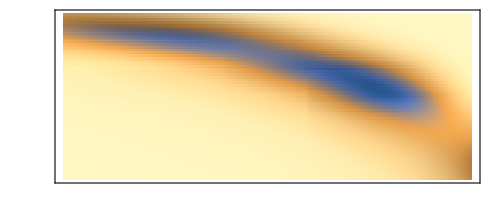

```mathematica
ReliefPlot[%105]
```

```mathematica
f[x_,y_]:=f[x,y]=
```

```mathematica
Plot3D[(%86[x,y])^21,{x,-0.9,-0.3},{y,-6.,-1.},Mesh->Automatic,MeshStyle->Directive[RGBColor[0.21,1,0.48],Opacity[0.6900000000000001],AbsoluteThickness[0.76],Dotted]]
```

-Graphics3D-

```mathematica
Plot3D[(%86[x,y])^21,{x,-0.9,-0.3},{y,-6.,-1.},MeshStyle->Directive[RGBColor[0.16,1.,0.37],Opacity[0.6900000000000001],AbsoluteThickness[0.76],Dashing[{0,Small}]],Mesh->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[(%86[x,y])^21,{x,-0.9,-0.3},{y,-6.,-1.},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Show[%91,Axes->False]
```

-Graphics3D-

```mathematica
Show[%92,Axes->True,AxesStyle->Black]
```

-Graphics3D-

```mathematica
Show[%93,Boxed->False]
```

-Graphics3D-

```mathematica
ListPlot3D[-%69]
```

-Graphics3D-

```mathematica
Interpolation[%46]
```

InterpolatingFunction[…]

```mathematica
Plot3D[%49[x,y],{x,0.3,0.9},{y,1.,6.}]
```

-Graphics3D-

```mathematica
Show[%50,Axes->False]
```

-Graphics3D-

```mathematica
Show[%51,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Plot3D[%42[x,y],{x,0.3,0.9},{y,1.,6.}]
```

-Graphics3D-

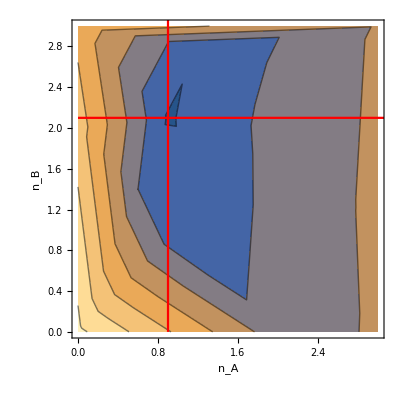

```mathematica
Show[%804,FrameLabel->{{HoldForm[Subscript[n, B]],None},{HoldForm[Subscript[n, A]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

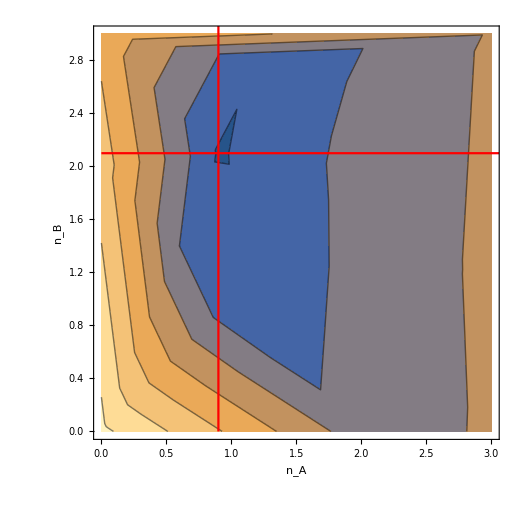

```mathematica
Show[%805,ImageSize->{520,500}]
```

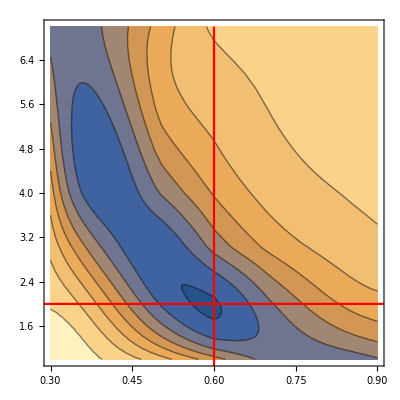

```mathematica
Show[ContourPlot[Interpolation[%784][x,y],{x,0.3,0.9},{y,1,7.}],ListLinePlot[{Table[{0.6,y},{y,Range[0,7.5,0.075]}],Table[{y,2},{y,Range[0,4,0.075]}]},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red},{Dashing[{1*^-2,0.01,0.01,1*^-2}],Red}},PlotRange->{{0,7},{0,7}},Frame->True]]
```

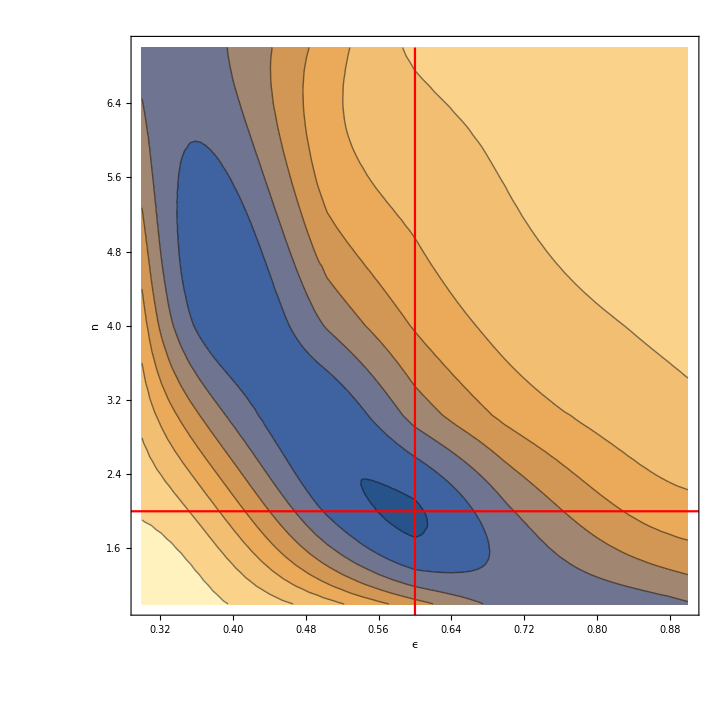

```mathematica
Show[%786,FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

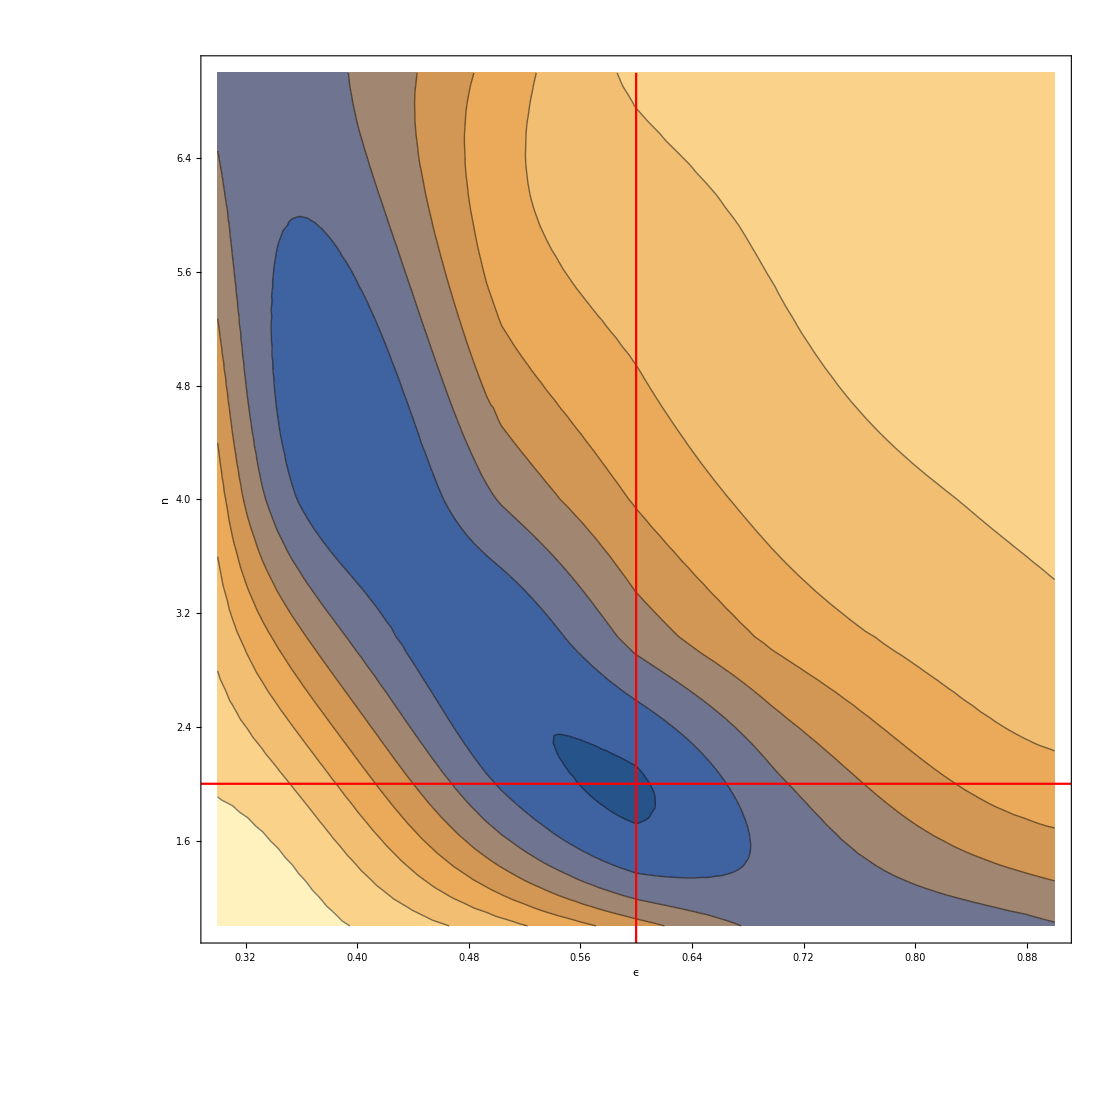

```mathematica
Show[%787,ImageSize->{500,500}]
```

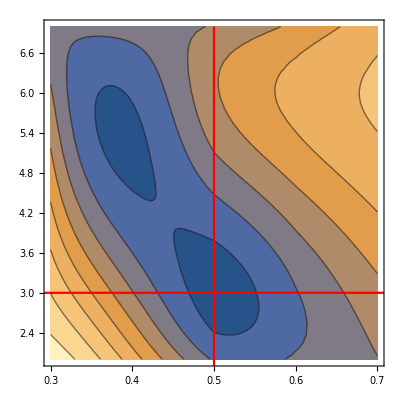

```mathematica
Show[ContourPlot[Interpolation[%597][x,y],{x,0.3,0.7},{y,2.,7.}],ListLinePlot[{Table[{0.5,y},{y,Range[0,7.5,0.075]}],Table[{y,3},{y,Range[0,4,0.075]}]},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red},{Dashing[{1*^-2,0.01,0.01,1*^-2}],Red}},PlotRange->{{1,7},{1,7}},Frame->True]]
```

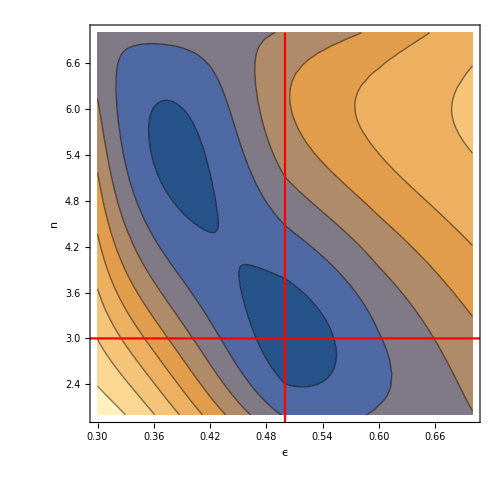

```mathematica
Show[%600,FrameLabel->{{HoldForm[n],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500}]
```

```mathematica
%597
```

{{0.3,1,-4.39164},{0.3,3,-5.25376},{0.3,5,-5.94978},{0.3,6,-6.21928},{0.4,1,-4.81935},{0.4,3,-6.23563},{0.4,5,-6.79833},{0.4,6,-6.72451},{0.5,1,-5.3224},{0.5,3,-6.86892},{0.5,5,-6.2917},{0.5,6,-6.03055},{0.6,1,-5.82487},{0.6,3,-6.51444},{0.6,5,-5.86292},{0.6,6,-5.68154},{0.7,1,-6.25047},{0.7,3,-6.0724},{0.7,5,-5.56752},{0.7,6,-5.46072},{0.8,1,-6.46419},{0.8,3,-5.77119},{0.8,5,-5.41624},{0.8,6,-5.3497},{0.9,1,-6.46645},{0.9,3,-5.5732},{0.9,5,-5.33465},{0.9,6,-5.29362}}

```mathematica
Show[%602,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
RandomSample[{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}]
```

{imp,imp,imp,imp6,imp4,imp10,imp,imp,imp14,imp11,imp,imp14,imp13,imp4,imp,imp7,imp,imp1,imp2,imp,imp,imp,imp,imp3,imp,imp6,imp13,imp,imp10,imp11,imp1,imp13,imp3,imp,imp,imp8,imp,imp7,imp,imp,imp,imp12,imp5,imp2,imp,imp5,imp3,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp7,imp,imp,imp,imp4,imp,imp9,imp12,imp,imp,imp,imp,imp2,imp,imp12,imp1,imp,imp,imp,imp,imp,imp6,imp14,imp,imp,imp9,imp,imp,imp,imp8,imp8,imp,imp,imp,imp9,imp,imp,imp10,imp,imp}

{{{2,0,-29.4753},{1.4,0.6,-33.2998},{1,1,-37.5327},{0.6,1.4,-40.0945},{0,2,-24.0271}},{{3,0,-26.1044},{2.1,0.9,-28.5491},{1.5,1.5,-31.936},{0.9,2.1,-37.4739},{0,3,-27.3961}},{{4,0,-24.7497},{2.8,1.2,-26.3359},{2,2,-28.6705},{1.2,2.8,-33.6722},{0,4,-30.0688}},{{0,0,-15.3595}},{{5,0,-24.086},{3.5,1.5,-25.1352},{2.5,2.5,-27.0029},{1.5,3.5,-30.9297},{0,5,-32.0961}}}

{{0,0,-15.3595},{0,2,-24.0271},{0,3,-27.3961},{0,4,-30.0688},{0,5,-32.0961},{0.6,1.4,-40.0945},{0.9,2.1,-37.4739},{1,1,-37.5327},{1.2,2.8,-33.6722},{1.4,0.6,-33.2998},{1.5,1.5,-31.936},{1.5,3.5,-30.9297},{2,0,-29.4753},{2,2,-28.6705},{2.1,0.9,-28.5491},{2.5,2.5,-27.0029},{2.8,1.2,-26.3359},{3,0,-26.1044},{3,3,-14},{3.5,1.5,-25.1352},{4,0,-24.7497},{5,0,-24.086}}

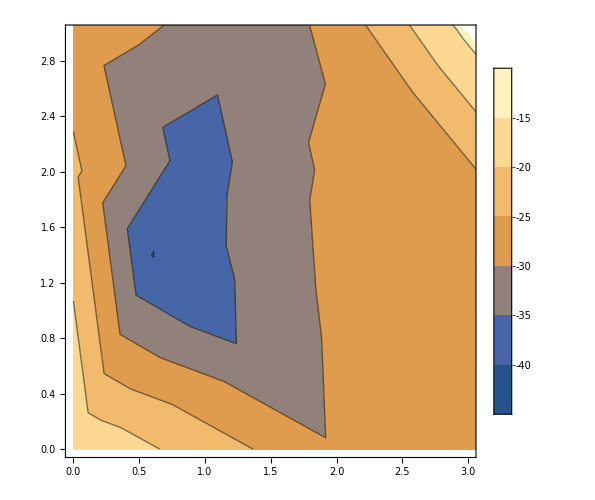

```mathematica
aa=misfit[0.3,0.9,0,1.49]
bb=Sort[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],{{3,3,-14}}]]
ListContourPlot[bb,PlotLegends->Automatic,PlotRange->{{0,3},{0,3}},ImageSize->{500,500}]
```

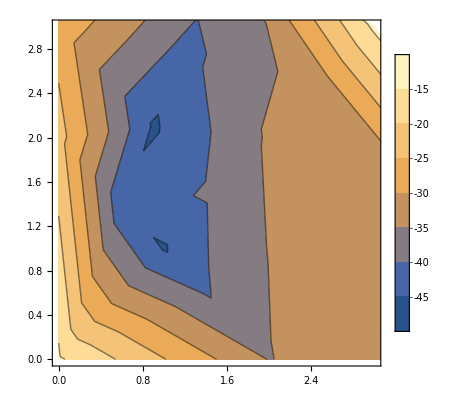

```mathematica
%180
```

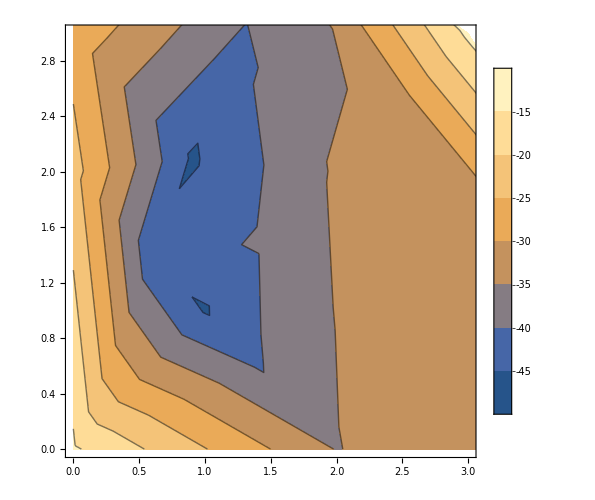

```mathematica
ListContourPlot[%179,PlotLegends->Automatic,PlotRange->{{0,3},{0,3}},ImageSize->{500,500}]
```

{{{2,0,-37.645},{1.4,0.6,-41.9788},{1,1,-44.3966},{0.6,1.4,-39.8667},{0,2,-22.2402}},{{3,0,-33.4891},{2.1,0.9,-36.9443},{1.5,1.5,-41.2622},{0.9,2.1,-45.4422},{0,3,-25.9611}},{{4,0,-31.4146},{2.8,1.2,-33.7477},{2,2,-37.2242},{1.2,2.8,-43.677},{0,4,-29.637}},{{0,0,-14.0051}},{{5,0,-30.3302},{3.5,1.5,-31.9828},{2.5,2.5,-34.6065},{1.5,3.5,-40.3318},{0,5,-33.0891}}}

{{0,0,-14.0051},{0,2,-22.2402},{0,3,-25.9611},{0,4,-29.637},{0,5,-33.0891},{0.6,1.4,-39.8667},{0.9,2.1,-45.4422},{1,1,-44.3966},{1.2,2.8,-43.677},{1.4,0.6,-41.9788},{1.5,1.5,-41.2622},{1.5,3.5,-40.3318},{2,0,-37.645},{2,2,-37.2242},{2.1,0.9,-36.9443},{2.5,2.5,-34.6065},{2.8,1.2,-33.7477},{3,0,-33.4891},{3,3,-14},{3.5,1.5,-31.9828},{4,0,-31.4146},{5,0,-30.3302}}

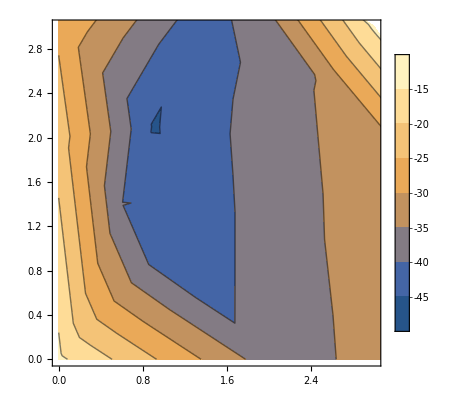

```mathematica
aa=misfit[0.3,0.9,0,1.49]
bb=Sort[Join[aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],{{3,3,-14}}]]
ListContourPlot[bb,PlotLegends->Automatic,PlotRange->{{0,3},{0,3}}]
```

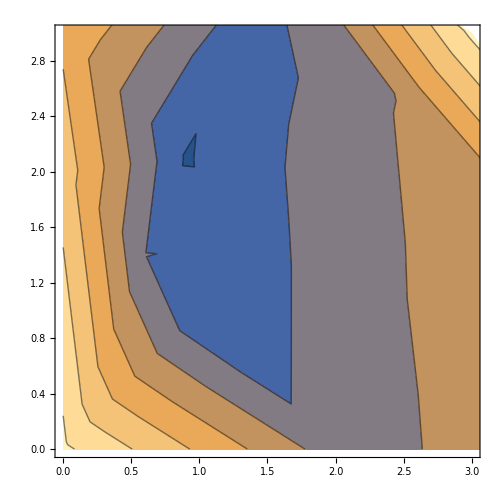

```mathematica
ListContourPlot[%164,PlotRange->{{0,3},{0,3}},ImageSize->{500,500}]
```

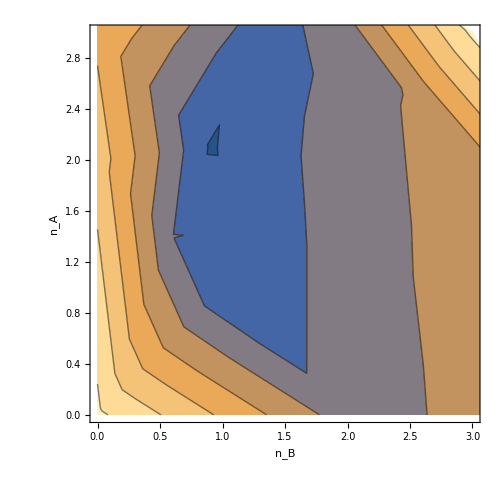

```mathematica
Show[%263,FrameLabel->{{HoldForm[Subscript[n, A]],None},{HoldForm[Subscript[n, B]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

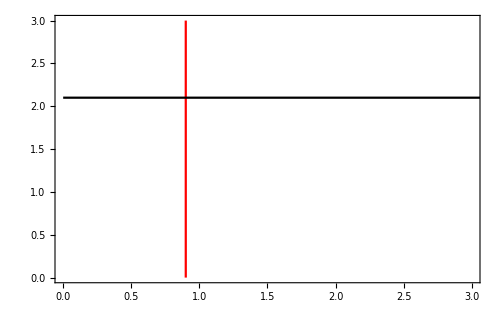

```mathematica
ListLinePlot[{Table[{0.9,y},{y,Range[0,3.2,0.075]}],Table[{y,2.1},{y,Range[0,3.2,0.075]}]},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red},{Dashing[{1*^-2,0.01,0.01,1*^-2}],Black}},ImageSize->{500,500},PlotRange->{{0,3},{0,3}},Frame->True]
```

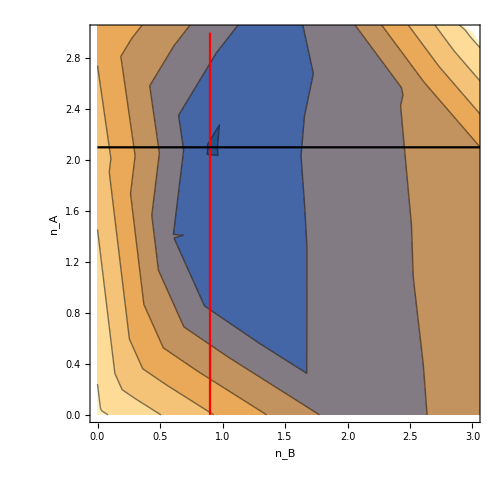

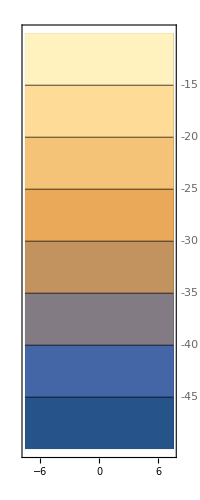
-Graphics- -Graphics-

```mathematica
Show[%265,%344,PlotLegends->Automatic]
```

```mathematica
Export["na_nb.eps",%350]
```

na_nb.eps

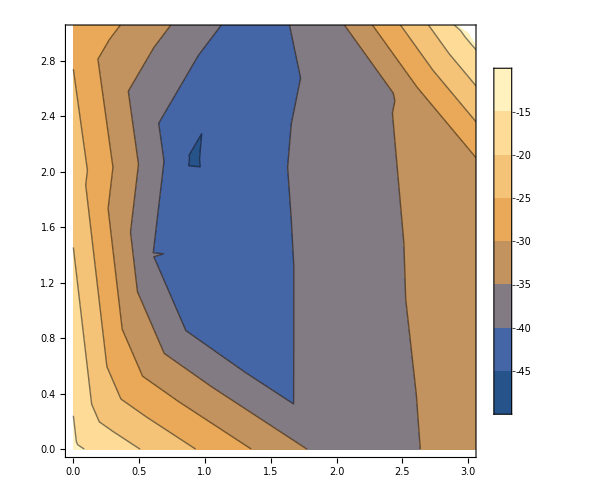

```mathematica
ListContourPlot[%164,PlotTheme->"Detailed",PlotRange->{{0,3},{0,3}},ImageSize->{500,500}]
```

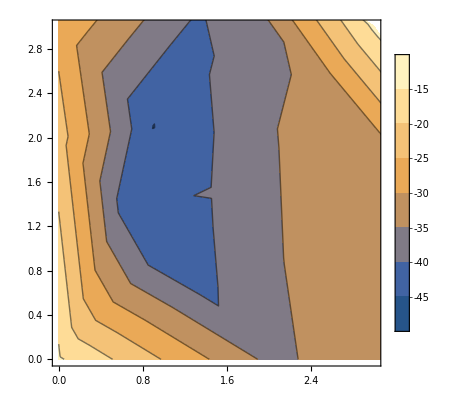

-Graphics-

```mathematica
ListInterpolation[%48]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction[…]

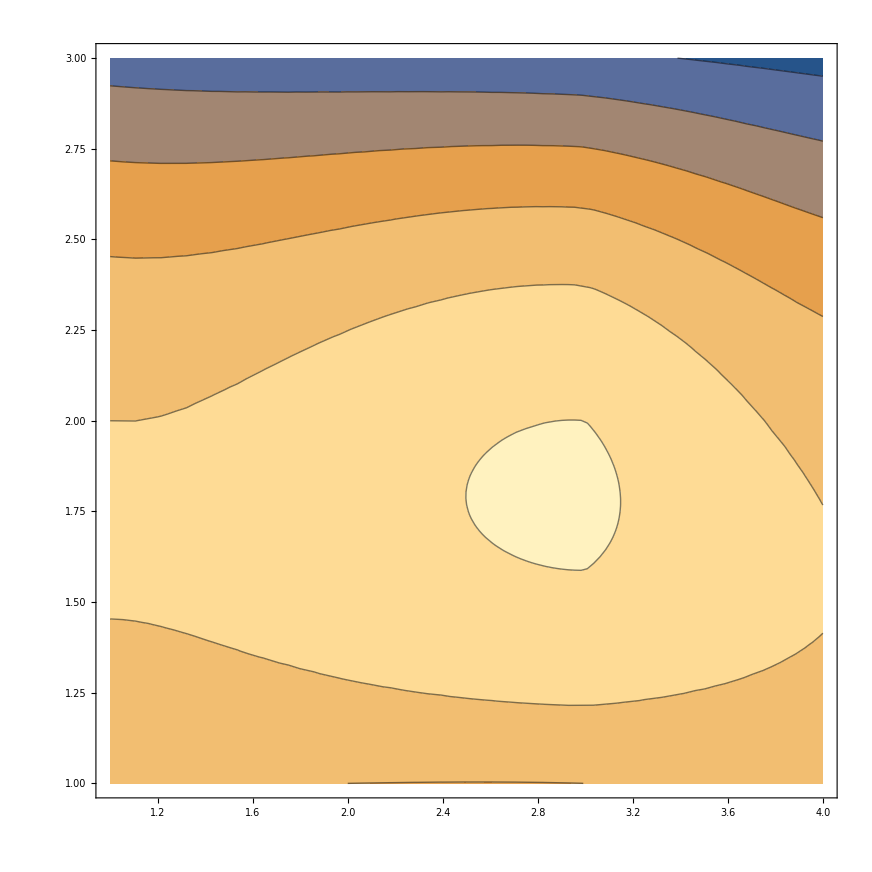

```mathematica
ContourPlot[%53[x,y],{x,1.,4.},{y,1.,3.}]
```

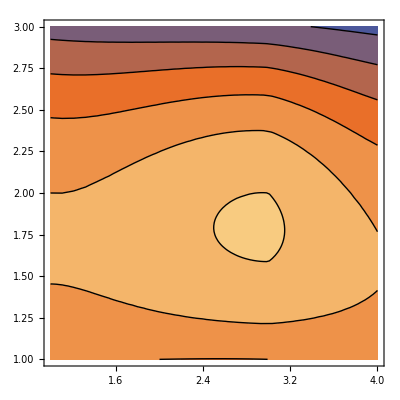

```mathematica
ContourPlot[%53[x,y],{x,1.,4.},{y,1.,3.},PlotTheme->"Scientific"]
```

```mathematica
Min[%28]
```

-6.91549

```mathematica
aa[[1]]
```

{{2,0,-6.11976},{1.4,0.6,-6.52422},{1,1,-6.85741},{0.6,1.4,-6.60868},{0,2,-4.83228}}

```mathematica
ListInterpolation[Join[aa[[1]],aa[[2]],aa[[3]]]]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction[…]

```mathematica
%38[0.9,2.1]
```

InterpolatingFunction::dmval: Input value {0.9,2.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.506682

```mathematica
Plot3D[%38[x,y],{x,1.,3.},{y,1.,3.}]
```

-Graphics3D-

InterpolatingFunction::dmval: Input value {0.000285714,0.000285714} lies outside the range of data in the interpolating function. Extrapolation will be used.

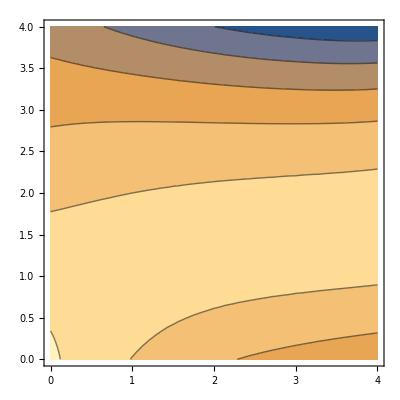

```mathematica
ContourPlot[%38[x,y],{x,0.,4.},{y,0.,4.}]
```

```mathematica
Min[%23]
```

-6.95108

```mathematica
Table[misfit[0.3,0.9,0,1.49][[2]],100]
```

{{0.0030617,0.00240891,0.00184133,0.00153089,0.00639676},{0.00326094,0.00246887,0.00179149,0.00132181,0.00623987},{0.0033042,0.00251871,0.00183322,0.00127052,0.00552117},{0.00389924,0.00292338,0.00198218,0.0011459,0.00538722},{0.00321099,0.00242388,0.00172961,0.00124494,0.00621229},{0.00503237,0.00383219,0.0026401,0.001454,0.00499892},{0.00365517,0.00280596,0.00203376,0.00140639,0.00636192},{0.00247548,0.00189339,0.00145122,0.00137933,0.00731786},{0.00295204,0.00259846,0.00232829,0.00227144,0.00644413},{0.00547846,0.00427091,0.0030529,0.00175914,0.00484808},{0.00300897,0.00225986,0.00164192,0.00132872,0.00655411},{0.00337221,0.00246706,0.00170151,0.00121365,0.00673622},{0.00305066,0.00243749,0.00190035,0.00163982,0.00698276},{0.00239512,0.0017526,0.00125676,0.00107108,0.00666688},{0.00459724,0.00357582,0.00256445,0.00157112,0.00513062},{0.00384073,0.00289788,0.00199817,0.00119276,0.00540684},{0.00272352,0.00192568,0.00126826,0.000958249,0.00696885},{0.00290871,0.00218819,0.0015522,0.00120885,0.00635083},{0.00319652,0.00267111,0.0021884,0.00188004,0.00641114},{0.00334314,0.00260371,0.00196978,0.00150281,0.00630961},{0.00342518,0.00273931,0.0021687,0.00186332,0.00695155},{0.00308117,0.00231023,0.00161569,0.00108167,0.00572348},{0.00422796,0.00322064,0.00224081,0.00132698,0.00538809},{0.00245602,0.00191535,0.00148461,0.00136825,0.00671053},{0.00397137,0.00299427,0.00202081,0.00105746,0.0046729},{0.0027111,0.00203416,0.00146637,0.00120398,0.00654304},{0.00300361,0.00236145,0.0018165,0.00157549,0.00680919},{0.0031911,0.00238562,0.00163602,0.00104597,0.00540848},{0.00295839,0.00220901,0.00154172,0.00115462,0.00660947},{0.00355123,0.00278451,0.0021567,0.0017464,0.00696741},{0.00284066,0.0021447,0.00149459,0.00104173,0.00585849},{0.00348862,0.00295947,0.00253182,0.00243349,0.00746691},{0.0028522,0.00216635,0.00158145,0.00130195,0.00669627},{0.00312202,0.00231309,0.00162945,0.00121481,0.00653612},{0.00361504,0.00266129,0.00178082,0.00111157,0.00600759},{0.00324525,0.0025429,0.00194371,0.00153842,0.00645928},{0.00275948,0.002146,0.00160652,0.00131693,0.00645852},{0.00278092,0.00222668,0.00180125,0.00164102,0.00710408},{0.00460456,0.00351332,0.002422,0.00125938,0.00427564},{0.00357433,0.00267643,0.00187031,0.00131918,0.00652362},{0.00300178,0.00235942,0.00175442,0.00133597,0.0060455},{0.00459724,0.00351312,0.00245542,0.0014366,0.00531224},{0.0034972,0.00291708,0.00249387,0.00236895,0.00823269},{0.00378742,0.00301781,0.0023904,0.0020155,0.00739226},{0.00359462,0.00268621,0.00183668,0.00116505,0.00580129},{0.00264048,0.00199664,0.00151821,0.00140589,0.00712748},{0.00277327,0.00203322,0.00140857,0.00108495,0.00653799},{0.00602108,0.00468973,0.003335,0.00181866,0.00432268},{0.00241982,0.00183582,0.00138855,0.00130633,0.0068301},{0.00316946,0.00235809,0.00170455,0.00135415,0.00698771},{0.00294475,0.0022819,0.00169434,0.0013602,0.00602447},{0.00428506,0.00347109,0.00277078,0.00237279,0.00779812},{0.00263068,0.00192616,0.00134966,0.00111368,0.00669747},{0.0024804,0.00189953,0.00143022,0.00128253,0.00671341},{0.00459879,0.00357793,0.00264713,0.0019324,0.00679382},{0.00279805,0.00229546,0.00188363,0.00168841,0.00649804},{0.00290564,0.00236287,0.00197228,0.00194869,0.007998},{0.00318967,0.00230388,0.00152313,0.00100724,0.00619184},{0.00295197,0.00254487,0.00219393,0.00209895,0.00657783},{0.00334292,0.00252711,0.00184356,0.00138611,0.00665782},{0.00315141,0.00252549,0.0019861,0.0017428,0.00693173},{0.00278865,0.0021641,0.0016355,0.00145779,0.00724448},{0.00242937,0.00188506,0.00144509,0.00130235,0.00668462},{0.00284224,0.00215284,0.00153276,0.00106428,0.00554775},{0.00355435,0.00291288,0.00230402,0.00180619,0.00567696},{0.00260696,0.00201361,0.00150638,0.00127412,0.00626163},{0.00302053,0.00249196,0.00210187,0.00203198,0.00785206},{0.0033534,0.00261147,0.00197285,0.00159651,0.00673773},{0.00342166,0.00253076,0.00173931,0.00119725,0.00639093},{0.00309927,0.00227082,0.00155727,0.00114291,0.00648189},{0.00276448,0.00222271,0.00177957,0.00164078,0.00687083},{0.00270348,0.00206916,0.00152128,0.00124847,0.00659179},{0.00282851,0.00208964,0.00139485,0.000895249,0.00558297},{0.00292881,0.00238242,0.00193984,0.00181075,0.00746758},{0.00370472,0.00287455,0.00209969,0.00138184,0.00521186},{0.00285398,0.00215976,0.00156884,0.00122992,0.00609555},{0.00385305,0.00285404,0.00191626,0.00113274,0.00579305},{0.00337587,0.00252957,0.00175752,0.00121245,0.0062183},{0.0031679,0.00254632,0.00201494,0.00170605,0.00658661},{0.00350168,0.00262155,0.0017884,0.00102514,0.00483839},{0.00343356,0.00287554,0.00244699,0.0022732,0.00765738},{0.00439227,0.00340628,0.00250207,0.00174477,0.00645019},{0.00285884,0.00208711,0.00138848,0.000950121,0.00607222},{0.00351479,0.00268121,0.00189914,0.00129974,0.00595868},{0.00324446,0.0023932,0.00164886,0.00116994,0.00650494},{0.00281997,0.00225109,0.00174634,0.00148603,0.00645109},{0.00302612,0.00238533,0.00188626,0.00172154,0.00739568},{0.00356186,0.00274351,0.00194626,0.00127258,0.00553024},{0.00567766,0.00445521,0.00324892,0.00191858,0.00479097},{0.00338362,0.00274045,0.00220467,0.00197708,0.00737717},{0.00340084,0.00254092,0.00171737,0.00100381,0.00510452},{0.00295975,0.00226783,0.00168128,0.00138355,0.00669228},{0.00345261,0.00265271,0.00194177,0.00143144,0.00653733},{0.00281162,0.00214879,0.001522,0.00107716,0.00563556},{0.00304027,0.00233598,0.00173234,0.00136328,0.006552},{0.00271335,0.00193191,0.00126512,0.000973076,0.00682309},{0.00279421,0.00206374,0.00142428,0.00106781,0.00645109},{0.00350915,0.00275696,0.00204441,0.0014819,0.00580492},{0.00312905,0.00248336,0.00188524,0.00138189,0.00569171},{0.00308867,0.00227199,0.00154014,0.00103812,0.00589269}}

```mathematica
Transpose[Join[{{0,0.3,0.5,0.7,1}},{Table[Mean[Table[%95[[x]][[y]],{x,100}]],{y,5}]}]]
```

{{0,0.00330621},{0.3,0.00255209},{0.5,0.00188364},{0.7,0.00143352},{1,0.00633398}}

```mathematica
Interpolation[%101]
```

InterpolatingFunction[…]

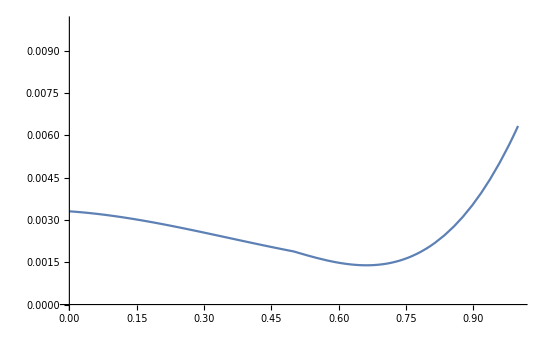

```mathematica
Plot[%102[x],{x,0,1.},PlotRange->{0,0.01}]
```

```mathematica
ListPlot[%77,Frame->True(*,PlotRange->{{0,0.3,0.5,0.7,1},{0,0.01}}*),PlotStyle->Directive[Blue,PointSize[0.01],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%79,FrameLabel->{{HoldForm[χ[Subscript[n, a],Subscript[n, b]]],None},{HoldForm[Subscript[n, b]/Subscript[n, a]],None}},PlotLabel->None,LabelStyle->{14,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics-

```mathematica
Show[%80,FrameLabel->{{HoldForm[χ[Subscript[n, a],Subscript[n, b]]],None},{HoldForm[HoldForm[Subscript[n, a]/(Subscript[n, b]+Subscript[n, a])]],None}},PlotLabel->HoldForm[For configurations with [Subscript[n, a]/(Subscript[n, b]+Subscript[n, a])]=0.7   Subscript[ϵ, a]=0.3 and Subscript[ϵ, b]=0.9],LabelStyle->{13,GrayLevel[0]},ImageSize->{500,500}]
```

-Graphics-

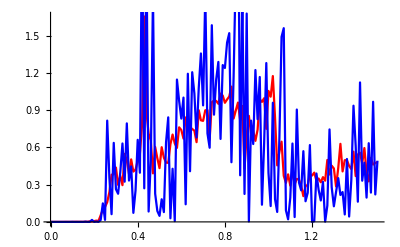

```mathematica
Show[%22,%25]
```

```mathematica
RandomReal[1,{10,3}]
```

```mathematica
{{0.21510125991701123,0.12569891244458642,-0.3528951454689433},{0.871265390123851,0.17186733000462473,0.5515596287046229},{0.13724887388424478,0.9097079861354329,0.45022175973491785},{0.15454909500848757,0.1967924331568225,0.09240021312450453},{0.7915213238773344,0.22113152239889056,0.27568864095813694},{0.7315927792084465,0.25825528346570636,0.36332617681073387},{0.3880265443560309,0.32167027209340193,-0.5704206115155126},{0.21795848866028833,0.20009400767901941,0.7537926589403585},{0.6951634597831031,0.8733860677207916,0.8065556151966107},{0.6220264376646418,0.010378064375728524,0.3326860976664219}}
```

{{0.215101,0.125699,-0.352895},{0.871265,0.171867,0.55156},{0.137249,0.909708,0.450222},{0.154549,0.196792,0.0924002},{0.791521,0.221132,0.275689},{0.731593,0.258255,0.363326},{0.388027,0.32167,-0.570421},{0.217958,0.200094,0.753793},{0.695163,0.873386,0.806556},{0.622026,0.0103781,0.332686}}

```mathematica
BubbleChart[%99]
```

-Graphics-

```mathematica
misfit[ϵ1_,ϵ2_,ϵ3_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp7,imp,imp,imp4,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp,imp3,imp,imp4,imp5,imp,imp,imp10,imp,imp,imp,imp,imp,imp1,imp2,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp6,imp,imp11,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp,imp,imp,imp3,imp14,imp,imp,imp5,imp,imp6,imp,imp,imp,imp9,imp9,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp12,imp,imp14,imp,imp,imp,imp8}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,If[tra1>3,3,tra1]},{ω,Range[0,1.5,0.01]}];
v1=Module[{},
ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/2/2na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/2/2na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={(*{2,0,ρ2},{1.4,0.6,ρ3},{1,1,ρ4},{0.6,1.4,ρ5},{0,2,ρ6},*){ρ2,ρ3,ρ4,ρ5,ρ6}};
list];v2=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/3/na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/3/na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{3,0,ρ2},{2,1,ρ3},{1.5,1.5,ρ4},{1,2,ρ5},{0,3,ρ6},{ρ2,ρ3,ρ4,ρ5,ρ6}};
list];v7=Module[{},ρ2=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim//PhD/fwi/7AGNR/two_imp/1/1na_0_nb_1439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_4_nb_1039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_7_nb_739.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_10_nb_439.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_14_nb_039.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={(*{1,0,ρ2},{1*0.7,1*0.3,ρ3},{.5,0.5,ρ4},{1*0.3,1*0.7,ρ5},{0,1,ρ6},*){ρ2,ρ3,ρ4,ρ5,ρ6}};
list];
{v7,v1,v2}]
```

```mathematica
Table[misfit[0.3,0.9,0,0.9,1.4][[2]][[1]],100]
```

{{0.00173084,0.00117887,0.000754582,0.000623447,0.00489534},{0.00202959,0.00149244,0.00104774,0.000842112,0.00465278},{0.00216966,0.00143359,0.000824549,0.000497277,0.00470436},{0.00231137,0.00183157,0.00141094,0.00114697,0.00431798},{0.00185483,0.00138075,0.00101613,0.000896562,0.00481359},{0.00283971,0.00236775,0.00193569,0.00153032,0.00381759},{0.00209871,0.00142815,0.000849252,0.000463136,0.00404173},{0.00198363,0.00142493,0.000982788,0.000807327,0.0048122},{0.00206711,0.00150629,0.0010112,0.00069196,0.00392707},{0.00356497,0.00258164,0.00170382,0.000991862,0.00439523},{0.00198618,0.00133586,0.000823302,0.000609914,0.00483846},{0.00183953,0.00114303,0.000619918,0.000441947,0.00496106},{0.00193314,0.00125635,0.000662344,0.000289162,0.00405057},{0.00228329,0.00153561,0.000895727,0.000514478,0.00454556},{0.00272107,0.00185447,0.00108607,0.000504911,0.00413461},{0.00291204,0.00219597,0.0014782,0.000761946,0.00279874},{0.0023443,0.00171524,0.00114895,0.00072381,0.00379646},{0.00273447,0.00189012,0.00109219,0.000373138,0.00307401},{0.00229768,0.00162083,0.00100089,0.000522686,0.00366178},{0.00159165,0.00101448,0.000570732,0.00043747,0.00479896},{0.00210472,0.00153876,0.00105112,0.000762366,0.00418297},{0.00192689,0.0013255,0.000812298,0.000492372,0.00389325},{0.00317069,0.00227458,0.00146676,0.000884854,0.00468218},{0.00178769,0.00122979,0.000743222,0.000490018,0.00430672},{0.00205064,0.00140486,0.000822921,0.000426229,0.00386083},{0.00237359,0.00163659,0.000978147,0.000452067,0.00355399},{0.00278,0.0019048,0.00113466,0.000588642,0.004302},{0.00219862,0.00146457,0.000835207,0.00043079,0.00431516},{0.00216318,0.00144635,0.000806333,0.000312147,0.00355338},{0.00216416,0.00144622,0.000804622,0.000330646,0.00361414},{0.00179418,0.0011709,0.000671624,0.000464984,0.00463752},{0.00228069,0.00149149,0.000843154,0.000443365,0.00432316},{0.00187094,0.00121107,0.000664663,0.00037656,0.00427579},{0.00161334,0.00110066,0.000672387,0.000503156,0.00446309},{0.00170741,0.00111076,0.000641554,0.000535023,0.0052403},{0.00171405,0.00115564,0.000687571,0.000491759,0.00466999},{0.0025028,0.00171569,0.00104901,0.000631615,0.00459689},{0.00211546,0.00143292,0.000825262,0.000416118,0.00402457},{0.0018639,0.0013722,0.000989495,0.000848161,0.00473861},{0.00194716,0.00128545,0.000753426,0.000530038,0.00485555},{0.00227817,0.00152911,0.000862452,0.000391977,0.00405184},{0.00248517,0.00164473,0.000913835,0.00038898,0.00406216},{0.00207553,0.00144098,0.000889652,0.000531562,0.00393734},{0.00216531,0.00144865,0.000823653,0.000411337,0.00403149},{0.00197144,0.00134793,0.000831102,0.000607341,0.00473731},{0.00198176,0.00125425,0.00067218,0.000393371,0.00471415},{0.00191415,0.00128106,0.000763892,0.000498735,0.00447723},{0.00201978,0.00132956,0.000737066,0.000358378,0.00396408},{0.00295287,0.00204304,0.00128883,0.000820434,0.00499763},{0.00206675,0.0015127,0.00103301,0.000737848,0.00418246},{0.00182069,0.00117749,0.000670516,0.000486532,0.00486108},{0.00177738,0.0011295,0.000590068,0.000362694,0.00472974},{0.0020598,0.00136466,0.000782315,0.00052191,0.00482119},{0.00295598,0.00208774,0.0013606,0.000946138,0.0052698},{0.00184007,0.00113813,0.000572728,0.000285541,0.00443356},{0.00228928,0.00164685,0.0010666,0.000606964,0.00380111},{0.00201151,0.00133839,0.000749038,0.000357005,0.00387688},{0.00252082,0.00172535,0.00100959,0.000491561,0.00406693},{0.00226903,0.00150138,0.000860134,0.000459077,0.00439129},{0.00196847,0.00126005,0.000697577,0.00045537,0.00481786},{0.0021014,0.0015414,0.00106498,0.000755801,0.00389434},{0.00182851,0.00126273,0.000805987,0.000628616,0.00476258},{0.00186947,0.00123977,0.000717198,0.00048788,0.00454811},{0.00196061,0.00129446,0.000719943,0.000426573,0.00478404},{0.00224809,0.00164764,0.0010649,0.000621646,0.00369707},{0.00179925,0.00126343,0.000839607,0.000705441,0.00469219},{0.0026388,0.00194642,0.00127454,0.000666545,0.00329064},{0.00247966,0.00188748,0.00133205,0.000827008,0.00334431},{0.00195756,0.00129067,0.000730308,0.000447628,0.00447251},{0.00233262,0.00158873,0.000973567,0.000607945,0.00461266},{0.0022681,0.00157824,0.000978275,0.00052393,0.00370709},{0.00308597,0.00253685,0.00197565,0.00141358,0.00336246},{0.00272332,0.00216072,0.00162254,0.00114275,0.00358069},{0.00229444,0.00154545,0.00088798,0.000410865,0.00379315},{0.00197957,0.00132052,0.000757488,0.000453342,0.0043319},{0.00264752,0.00181258,0.0010743,0.000496698,0.00377568},{0.00195967,0.00142631,0.000945042,0.000701927,0.0043695},{0.00347967,0.00246141,0.00152939,0.00072646,0.00385876},{0.00292135,0.00202332,0.00121518,0.000583025,0.00406494},{0.0022409,0.00157284,0.000949143,0.000470142,0.00376438},{0.00308893,0.00249047,0.00188957,0.00127143,0.0033931},{0.00196815,0.00135531,0.000823755,0.000496303,0.00420894},{0.00215316,0.00158417,0.0010949,0.000804711,0.00425932},{0.00196481,0.00132104,0.000760503,0.000449709,0.00429185},{0.0027687,0.00194415,0.00115522,0.000463367,0.00319904},{0.00231654,0.00172793,0.00121483,0.000849919,0.00394891},{0.0019428,0.00129494,0.000761061,0.000498378,0.00471028},{0.00210281,0.00151353,0.00100327,0.000680579,0.00425558},{0.00192013,0.00135433,0.00085554,0.000623,0.0045153},{0.00276647,0.00188563,0.00109853,0.000453895,0.00373569},{0.00235094,0.0015801,0.000888819,0.000395501,0.00397914},{0.0027144,0.00188565,0.00119682,0.000805135,0.00508856},{0.00241332,0.00162434,0.000943518,0.000475276,0.00420637},{0.00277723,0.00204905,0.00138293,0.000784654,0.00351092},{0.00189787,0.00130972,0.00084498,0.00064801,0.00460823},{0.00183508,0.0012146,0.000712384,0.000467862,0.00461112},{0.0020858,0.00140024,0.000831297,0.000492829,0.00432007},{0.00293828,0.00203934,0.00127105,0.000727999,0.00452834},{0.00273649,0.00187381,0.00110095,0.00049781,0.00378467},{0.00245065,0.00168796,0.0010126,0.000490013,0.00379213}}

```mathematica
Table[100*Around[Table[%121[[x]][[y]], {x, 100}]],{y,5}]
```

```mathematica
{{0,0.220.04},{0.3,0.1570.035},{0.5,0.0980.029},{0.7,0.0600.023},{1,0.420.05}}
```

{{0,0.220.04},{0.3,0.1570.035},{0.5,0.0980.029},{0.7,0.0600.023},{1,0.420.05}}

```mathematica
ListPlot[%130,Frame->True,FrameTicks->{{None,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Green,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%131,%128,PlotRange->All,FrameLabel->{{HoldForm[χ],None},{HoldForm[Subscript[n, a]/Subscript[n, b]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%1,FrameLabel->{{HoldForm[χ],None},{HoldForm[HoldForm[Subscript[n, A]/(Subscript[n, B]+Subscript[n, A])]],None}},PlotLabel->None]
```

-Graphics-

```mathematica
{{0,0.0620.018},{0.3,0.0540.015},{0.5,0.0700.021},{0.7,0.160.04},{1,0.870.07}}
```

```mathematica
{{0,0.0620.018+0.02},{0.3,0.0540.015},{0.5,0.0700.021+0.02},{0.7,0.160.04},{1,0.870.07}}
```

{{0,0.0820.018},{0.3,0.0540.015},{0.5,0.0900.021},{0.7,0.160.04},{1,0.870.07}}

```mathematica
ListPlot[%127,Frame->True,FrameTicks->{{None,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Table[100*Around[Table[%85[[x]][[y]], {x, 100}]],{y,5}]
```

{0.1020.025,0.0700.018,0.0580.017,0.0990.025,0.690.05}

```mathematica
{%87}
```

```mathematica
{{0,0.1020.025},{0.3,0.0700.018},{0.5,0.0580.017},{0.7,0.0990.025},{1,0.690.05}}
```

{{0,0.1020.025},{0.3,0.0700.018},{0.5,0.0580.017},{0.7,0.0990.025},{1,0.690.05}}

```mathematica
ListPlot[%99,Frame->True,FrameTicks->{{None,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Black,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%110,%109,PlotRange->All]
```

-Graphics-

```mathematica
Show[%117,FrameLabel->{{HoldForm[χ],None},{HoldForm[Subscript[n, a]/Subscript[n, b]],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
{%75}
```

```mathematica
{{0,1.000.05},{0.3,0.840.05},{0.5,0.660.04},{0.7,0.4000.029},{1,0.0260.008}}
```

{{0,1.000.05},{0.3,0.840.05},{0.5,0.660.04},{0.7,0.4000.029},{1,0.0260.008}}

```mathematica
ListPlot[%103,Frame->True,FrameTicks->{{None,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Table[100*Around[Table[%70[[x]][[y]], {x, 100}]],{y,5}]
```

{0.0450.013,0.0550.012,0.0920.019,0.2100.033,0.990.07}

```mathematica
{%71}
```

```mathematica
{{0,0.0450.013},{0.3,0.0550.012},{0.5,0.0920.019},{0.7,0.2100.033},{1,0.990.07}}
```

{{0,0.0450.013},{0.3,0.0550.012},{0.5,0.0920.019},{0.7,0.2100.033},{1,0.990.07}}

```mathematica
ListPlot[%106,Frame->True,FrameTicks->{{None,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Red,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%80,%86,%91]
```

-Graphics-

```mathematica
Show[%92,FrameTicks->{{Automatic,None},{Automatic,None}}]
```

-Graphics-

```mathematica
Table[100*Around[Table[%50[[x]][[y]], {x, 100}]],{y,5}]
```

{0.220.04,0.1510.035,0.0950.030,0.0630.027,0.450.06}

```mathematica
ListPlot[%67,Frame->True,FrameTicks->{{None,None},{{None},None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-